```mathematica
(*ρ = Subscript[λ, m2]/Subscript[λ, m1];
α = (Subscript[λ, p] Subscript[λ, m1])/(Subscript[d, p] Subscript[d, m]);*)

params = {Subscript[λ, p]->2,Subscript[λ, m1]->2, Subscript[λ, m2]-> 18,Subscript[d, p]->0.08,Subscript[d, m]->0.5,n->4, ρ ->9,α ->100};
k =  p(ρ/(p/α-1)-1)^(1/n);
```

```mathematica
a=α((n+1)ρ + 2n-(n+1)(ρ(ρ-4 n/(n+1)^2))^0.5)/(2n)
b= α((n+1)ρ + 2n+(n+1)(ρ(ρ-4 n/(n+1)^2))^0.5)/(2n)
```

(α (2 n+(1+n) ρ-(1+n) (ρ (-(4 n)/(1+n)^2+ρ))^0.5))/(2 n)

(α (2 n+(1+n) ρ+(1+n) (ρ (-(4 n)/(1+n)^2+ρ))^0.5))/(2 n)

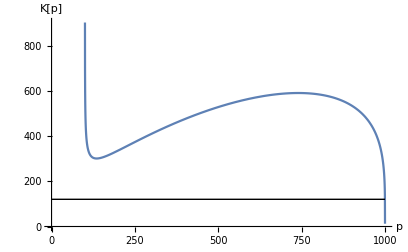

```mathematica
pl1 = Plot[k /. params, {p,0,1000}, AxesLabel->{"p", "K[p]"}];
l1=Graphics@Line[{{0, a /.params},{1000,a /.params}}];
l2=Graphics@Line[{{0,b/.params},{1000,b/.params}}];
Show[pl1,l1, l2]
```

```mathematica
b /. params
```

1204.63

```mathematica
Manipulate[
params = {Subscript[λ, p]->lamPval,Subscript[λ, m1]->lamM1val, Subscript[λ, m2]-> lamM2val,Subscript[d, p]->dpval,Subscript[d, m]->dmval,n->nval};
Plot[p((Subscript[λ, m2]/Subscript[λ, m1])/(p/((Subscript[λ, p] Subscript[λ, m1])/(Subscript[d, p] Subscript[d, m])-1))-1)^(1/n)/.params, {p,0,500}, AxesLabel-> {"p", "K[p]"}],
{{lamPval, 2},0.1,10,Appearance->"Labeled"},
{{lamM1val,2},0.1,10,Appearance->"Labeled"},
{{lamM2val,18},0.1,10,Appearance->"Labeled"},
{{dpval,0.08},0.1,10,Appearance->"Labeled"},
{{dmval,0.5},0.1,10,Appearance->"Labeled"},
{{nval,4},0.1,10,Appearance->"Labeled"}
];
```